```mathematica
ψ[t_]:=ψ0+ψ1[t] ξ+ψ2[t] ξ^2+ψ3[t]ξ^3+ψ4[t] ξ^4+O[ξ]^5;
```

```mathematica
s=1/2+s2 ξ^2+s3 ξ^3+s4 ξ^4+s5 ξ^5+O[ξ]^6;d=d0+δ ξ^2;ψmax=p0+p1 ξ+p2 ξ^2+p3 ξ^3+p4 ξ^4+O[ξ]^5;Λ=1+Λ1 ξ+Λ2 ξ^2+Λ3 ξ^3+Λ4 ξ^4+O[ξ]^5;μ=μ0+μ1 ξ+μ2 ξ^2+μ3 ξ^3+μ4 ξ^4+O[ξ]^5;
```

```mathematica
l0=Sqrt[1/(ξ r)];
```

```mathematica
eq =Simplify[4 μ Sin[ψ[t]]/(ξ^2(1+μ Cos[ψ[t]])) (-1+ψ'[t]^2 ξ^2/(8(1-2 s)^2)) -ψ''[t]/(1-2s)^2+O[ξ]^3]
```

-ψ1''[t]/(4 s2^2 ξ^3)+((4 μ0 Sin[ψ0] (-1+ψ1'[t]^2/(32 s2^2)))/(1+μ0 Cos[ψ0])+(s3 ψ1''[t])/(2 s2^3)-ψ2''[t]/(4 s2^2))/ξ^2+1/(8 s2^4 (1+μ0 Cos[ψ0])^2 ξ)(s2 (-2 s3 μ0+s2 μ1-2 s3 μ0^2 Cos[ψ0]) Sin[ψ0] ψ1'[t]^2-s2^2 μ0 (μ0+Cos[ψ0]) ψ1[t] (32 s2^2-ψ1'[t]^2)+2 s2^2 μ0 (1+μ0 Cos[ψ0]) Sin[ψ0] ψ1'[t] ψ2'[t]-2 ((3 s3^2-2 s2 s4) (1+μ0 Cos[ψ0])^2 ψ1''[t]+s2 (-2 s3 (1+μ0 Cos[ψ0])^2 ψ2''[t]+s2 (16 s2^2 μ1 Sin[ψ0]+(1+μ0 Cos[ψ0])^2 ψ3''[t]))))+1/(16 s2^5)(1/(1+μ0 Cos[ψ0])^3 s2 (-1/2 s2^2 μ0 (-2 (μ2+(-μ1^2+μ0 μ2) Cos[ψ0]) Sin[2 ψ0]-4 μ1 (μ0 Cos[ψ0]+Cos[2 ψ0]) ψ1[t]+2 (-1+2 μ0^2+μ0 Cos[ψ0]) Sin[ψ0] ψ1[t]^2+2 (2 (1+μ0^2) Cos[ψ0]+μ0 (3+Cos[2 ψ0])) ψ2[t]) (32 s2^2-ψ1'[t]^2)+s2 (1+μ0 Cos[ψ0]) (μ1 Sin[2 ψ0]-2 (μ0+Cos[ψ0]) ψ1[t]) (32 s2^3 μ1+(2 s3 μ0-s2 μ1) ψ1'[t]^2-2 s2 μ0 ψ1'[t] ψ2'[t])-2 (1+μ0 Cos[ψ0])^2 Sin[ψ0] (32 s2^4 μ2+(-3 s3^2 μ0+2 s2 s3 μ1+s2 (2 s4 μ0-s2 μ2)) ψ1'[t]^2-s2^2 μ0 ψ2'[t]^2-2 s2 ψ1'[t] ((-2 s3 μ0+s2 μ1) ψ2'[t]+s2 μ0 ψ3'[t])))+8 (2 s3^3-3 s2 s3 s4+s2^2 s5) ψ1''[t]+4 s2 (-3 s3^2+2 s2 s4) ψ2''[t]+8 s2^2 s3 ψ3''[t]-4 s2^3 ψ4''[t])+O[ξ]^1

```mathematica
bc1=Simplify[ψ[t] - ψmax s/.t->0]
```

(-p0/2+ψ0)+(-p1/2+ψ1[0]) ξ+(-p2/2-p0 s2+ψ2[0]) ξ^2+(-p3/2-p1 s2-p0 s3+ψ3[0]) ξ^3+(-p4/2-p2 s2-p1 s3-p0 s4+ψ4[0]) ξ^4+O[ξ]^5

```mathematica
bc2=Simplify[ψ'[t] - (1-2s)ψmax/.t->0]
```

ψ1'[0] ξ+(2 p0 s2+ψ2'[0]) ξ^2+(2 p1 s2+2 p0 s3+ψ3'[0]) ξ^3+(2 p2 s2+2 p1 s3+2 p0 s4+ψ4'[0]) ξ^4+O[ξ]^5

```mathematica
bc3=Simplify[ψ'[t]/.t->1/2]
```

ψ1'[1/2] ξ+ψ2'[1/2] ξ^2+ψ3'[1/2] ξ^3+ψ4'[1/2] ξ^4+O[ξ]^5

```mathematica
Simplify[Sin[ψmax s]/ψmax( 1+ξ^2 ψmax^2/8)+ Integrate[Cos[ψ[t]](1+ξ^2/8 (ψ'[t])^2/(1-2 s)^2)(1-2s),{t,0,1/2}]- Λ(1-d)/2]
```

∫_0^(1/2) (-2 (s2 Cos[ψ0] (1+ψ1'[t]^2/(32 s2^2))) ξ^2+((s2 Sin[ψ0] ψ1[t] (32 s2^2+ψ1'[t]^2)+Cos[ψ0] (-32 s2^2 s3+s3 ψ1'[t]^2-2 s2 ψ1'[t] ψ2'[t])) ξ^3)/(16 s2^2)+1/(32 s2^3)(s2^2 Cos[ψ0] ψ1[t]^2 (32 s2^2+ψ1'[t]^2)+2 s2^2 Sin[ψ0] ψ2[t] (32 s2^2+ψ1'[t]^2)+2 s2 Sin[ψ0] ψ1[t] (32 s2^2 s3-s3 ψ1'[t]^2+2 s2 ψ1'[t] ψ2'[t])-2 Cos[ψ0] ((s3^2-s2 s4) ψ1'[t]^2+s2^2 (32 s2 s4+ψ2'[t]^2)+2 s2 ψ1'[t] (-s3 ψ2'[t]+s2 ψ3'[t]))) ξ^4+1/(96 s2^4)(-s2^3 Sin[ψ0] ψ1[t]^3 (32 s2^2+ψ1'[t]^2)+3 s2^2 Cos[ψ0] ψ1[t]^2 (32 s2^2 s3-s3 ψ1'[t]^2+2 s2 ψ1'[t] ψ2'[t])+6 s2 ψ1[t] (s2^2 Cos[ψ0] ψ2[t] (32 s2^2+ψ1'[t]^2)+Sin[ψ0] ((s3^2-s2 s4) ψ1'[t]^2+s2^2 (32 s2 s4+ψ2'[t]^2)+2 s2 ψ1'[t] (-s3 ψ2'[t]+s2 ψ3'[t])))+6 (s2^3 Sin[ψ0] ψ3[t] (32 s2^2+ψ1'[t]^2)+s2^2 Sin[ψ0] ψ2[t] (32 s2^2 s3-s3 ψ1'[t]^2+2 s2 ψ1'[t] ψ2'[t])+Cos[ψ0] ((s3^3-2 s2 s3 s4+s2^2 s5) ψ1'[t]^2+s2^2 (-32 s2^2 s5+s3 ψ2'[t]^2-2 s2 ψ2'[t] ψ3'[t])-2 s2 ψ1'[t] ((s3^2-s2 s4) ψ2'[t]+s2 (-s3 ψ3'[t]+s2 ψ4'[t]))))) ξ^5+O[ξ]^6)ⅆt+((1/2 (-1+d0)+Sin[p0/2]/p0)+(((-1+d0) p0^2 Λ1+p0 p1 Cos[p0/2]-2 p1 Sin[p0/2]) ξ)/(2 p0^2)+1/(8 p0^3)(4 p0^3 (δ+(-1+d0) Λ2)+4 p0 (-p1^2+p0 (p2+2 p0 s2)) Cos[p0/2]+(p0^4+8 p1^2-p0^2 p1^2-8 p0 p2) Sin[p0/2]) ξ^2+1/(48 p0^4)(p0 (3 p0^4 p1+24 p1^3-48 p0 p1 p2-p0^2 (p1^3-24 p3)+48 p0^3 s3) Cos[p0/2]+6 (4 p0^4 (δ Λ1+(-1+d0) Λ3)+(-8 p1^3+16 p0 p1 p2-2 p0^3 p1 p2+p0^2 (p1^3-8 p3)+p0^4 (p1-4 p1 s2)) Sin[p0/2])) ξ^3+1/(384 p0^5)(192 p0^5 (δ Λ2+(-1+d0) Λ4)+8 p0 (-24 p1^4+3 p0^5 p2+72 p0 p1^2 p2+p0^2 (p1^4-24 p2^2-48 p1 p3)-3 p0^3 (p1^2 p2-8 p4)+6 p0^6 s2+p0^4 (p1^2 (3-6 s2)+48 s4)) Cos[p0/2]-(-384 p1^4+1152 p0 p1^2 p2+48 p0^2 (p1^4-8 p2^2-16 p1 p3)+p0^4 (-p1^4+48 p2^2+96 p1 p3)-48 p0^3 (3 p1^2 p2-8 p4)+6 p0^6 (p1^2+32 s2^2)+48 p0^5 (-p2+4 p2 s2+4 p1 s3)) Sin[p0/2]) ξ^4+O[ξ]^5)

```mathematica
bc4=Simplify[(1/2 (-1+d0)+Sin[p0/2]/p0)+ξ(((-1+d0) p0^2 Λ1+p0 p1 Cos[p0/2]-2 p1 Sin[p0/2])/(2 p0^2))+ξ^2(1/(8 p0^3)(4 p0^3 (δ+(-1+d0) Λ2)+4 p0 (-p1^2+p0 (p2+2 p0 s2)) Cos[p0/2]+(p0^4+8 p1^2-p0^2 p1^2-8 p0 p2) Sin[p0/2])+Integrate[-2 (s2 Cos[ψ0] (1+ψ1'[t]^2/(32 s2^2))) ,{t,0,1/2}])+ξ^3(Integrate[(s2 Sin[ψ0] ψ1[t] (32 s2^2+ψ1'[t]^2)+Cos[ψ0] (-32 s2^2 s3+s3 ψ1'[t]^2-2 s2 ψ1'[t] ψ2'[t]))/(16 s2^2),{t,0,1/2}]+1/(48 p0^4)(p0 (3 p0^4 p1+24 p1^3-48 p0 p1 p2-p0^2 (p1^3-24 p3)+48 p0^3 s3) Cos[p0/2]+6 (4 p0^4 (δ Λ1+(-1+d0) Λ3)+(-8 p1^3+16 p0 p1 p2-2 p0^3 p1 p2+p0^2 (p1^3-8 p3)+p0^4 (p1-4 p1 s2)) Sin[p0/2])))+O[ξ]^4]
```

(1/2 (-1+d0)+Sin[p0/2]/p0)+(((-1+d0) p0^2 Λ1+p0 p1 Cos[p0/2]-2 p1 Sin[p0/2]) ξ)/(2 p0^2)+(∫_0^(1/2) -2 s2 Cos[ψ0] (1+ψ1'[t]^2/(32 s2^2))ⅆt+(4 p0^3 (δ+(-1+d0) Λ2)+4 p0 (-p1^2+p0 (p2+2 p0 s2)) Cos[p0/2]+(p0^4+8 p1^2-p0^2 p1^2-8 p0 p2) Sin[p0/2])/(8 p0^3)) ξ^2+(∫_0^(1/2) (s2 Sin[ψ0] ψ1[t] (32 s2^2+ψ1'[t]^2)+Cos[ψ0] (-32 s2^2 s3+s3 ψ1'[t]^2-2 s2 ψ1'[t] ψ2'[t]))/(16 s2^2)ⅆt+1/(48 p0^4)(p0 (3 p0^4 p1+24 p1^3-48 p0 p1 p2-p0^2 (p1^3-24 p3)+48 p0^3 s3) Cos[p0/2]+6 (4 p0^4 (δ Λ1+(-1+d0) Λ3)+(-8 p1^3+16 p0 p1 p2-2 p0^3 p1 p2+p0^2 (p1^3-8 p3)+p0^4 (p1-4 p1 s2)) Sin[p0/2]))) ξ^3+O[ξ]^4

```mathematica
dψmax=Simplify[(- l0^2ψmax^3/16 ξ^3+ψmax^2 ξ^2/(24 Λ^2)+l0^2ψmax ξ/2+1/Λ^2)/(3Λ l0^2 ξ^3ψmax^2/16+ψmax ξ^2/(12 Λ)-l0^2 Λ ξ/2)]
```

(-p0-2 r)+(-p1+(p0+6 r) Λ1) ξ+(-p0^3/4-p2-p0^2 r+p1 Λ1-12 r Λ1^2+6 r Λ2+p0 (-r^2/3-Λ1^2+Λ2)) ξ^2+(-p3-(p1 r^2)/3+(p0^3 Λ1)/4+p2 Λ1-p1 Λ1^2+20 r Λ1^3-3/4 p0^2 (p1-4 r Λ1)+p1 Λ2-24 r Λ1 Λ2+6 r Λ3+p0 (-2 p1 r+(5 r^2 Λ1)/3+Λ1^3-2 Λ1 Λ2+Λ3)) ξ^3+(-(3 p0^5)/32-p4-(5 p0^4 r)/12-p1^2 r-(p2 r^2)/3+p3 Λ1+5/3 p1 r^2 Λ1-p2 Λ1^2+p1 Λ1^3-30 r Λ1^4-1/24 p0^3 (7 r^2+6 Λ1^2-6 Λ2)+p2 Λ2-2 p1 Λ1 Λ2+60 r Λ1^2 Λ2-12 r Λ2^2+p0^2 (-(3 p2)/4-r^3/18+(3 p1 Λ1)/4-6 r Λ1^2+3 r Λ2)+p1 Λ3-24 r Λ1 Λ3+6 r Λ4+p0 (-(3 p1^2)/4-2 p2 r+6 p1 r Λ1-5 r^2 Λ1^2-Λ1^4+(5 r^2 Λ2)/3+3 Λ1^2 Λ2-Λ2^2-2 Λ1 Λ3+Λ4)) ξ^4+O[ξ]^5

```mathematica
Simplify[1-1/Λ^2+ξ^2 s/4(-ψmax^2/Λ^2+2 ψmax dψmax/Λ)-Integrate[ψ'[t]^2ξ^2/(4Λ^2(1-2s)),{t,0,1/2}]-μ(1-d)/Λ-2μ(Sin[ψmax s]/(Λ ψmax^2)dψmax(1-ψmax^2ξ^2/8)-Cos[ψmax s]/(Λ ψmax)s dψmax(1+ψmax^2 ξ^2/8))+O[ξ]^4]
```

-∫_0^(1/2) (-(ψ1'[t]^2 ξ^2)/(8 s2)+(ψ1'[t] ((s3+2 s2 Λ1) ψ1'[t]-2 s2 ψ2'[t]) ξ^3)/(8 s2^2)-1/(8 s2^3)((s3^2+2 s2 s3 Λ1+s2 (-s4+3 s2 Λ1^2-2 s2 Λ2)) ψ1'[t]^2+s2^2 ψ2'[t]^2-2 s2 ψ1'[t] ((s3+2 s2 Λ1) ψ2'[t]-s2 ψ3'[t])) ξ^4+1/(8 s2^4)((s3^3+2 s2 s3^2 Λ1+s2 s3 (-2 s4+3 s2 Λ1^2-2 s2 Λ2)+s2^2 (s5-2 s4 Λ1+2 s2 (2 Λ1^3-3 Λ1 Λ2+Λ3))) ψ1'[t]^2+s2^2 ψ2'[t] ((s3+2 s2 Λ1) ψ2'[t]-2 s2 ψ3'[t])-2 s2 ψ1'[t] ((s3^2+2 s2 s3 Λ1+s2 (-s4+3 s2 Λ1^2-2 s2 Λ2)) ψ2'[t]+s2 (-((s3+2 s2 Λ1) ψ3'[t])+s2 ψ4'[t]))) ξ^5+O[ξ]^6)ⅆt+((μ0 ((-1+d0) p0^2-p0 (p0+2 r) Cos[p0/2]+2 (p0+2 r) Sin[p0/2]))/p0^2+(Λ1 (2+μ0-d0 μ0)+(-1+d0) μ1+((4 p1 r μ0+p0^2 (2 Λ1 μ0-μ1)+p0 (p1 μ0+8 r Λ1 μ0-2 r μ1)) Cos[p0/2])/p0^2+((p0^3 p1 μ0-16 p1 r μ0+2 p0^2 (p1 r μ0-4 Λ1 μ0+2 μ1)-4 p0 (p1 μ0+8 r Λ1 μ0-2 r μ1)) Sin[p0/2])/(2 p0^3)) ξ-1/(24 p0^4)(3 p0^4 (3 p0^2+4 p0 r-8 (δ μ0+Λ1^2 (-3+(-1+d0) μ0)+Λ2 (2+μ0-d0 μ0)+Λ1 (μ1-d0 μ1)-μ2+d0 μ2))+p0 (9 p0^5 μ0+30 p0^4 r μ0+144 p1^2 r μ0+24 p0 (p1^2 μ0-4 p2 r μ0+4 p1 r (4 Λ1 μ0-μ1))-6 p0^2 (4 p2 μ0+p1^2 r μ0+p1 (-8 Λ1 μ0+4 μ1)-8 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2))+p0^3 (-3 p1^2 μ0+8 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2))) Cos[p0/2]-2 (144 p1^2 r μ0+3 p0^5 (μ0+4 s2 μ0)+24 p0 (p1^2 μ0-4 p2 r μ0+4 p1 r (4 Λ1 μ0-μ1))+6 p0^4 (p2 μ0+r (3+4 s2) μ0+p1 (-2 Λ1 μ0+μ1))-6 p0^2 (4 p2 μ0+3 p1^2 r μ0+p1 (-8 Λ1 μ0+4 μ1)-8 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2))+p0^3 (-3 p1^2 μ0+12 p2 r μ0+12 p1 r (-4 Λ1 μ0+μ1)+8 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2))) Sin[p0/2]) ξ^2+1/(48 p0^5)(12 p0^5 (-2 p1 r+3 p0^2 Λ1+p0 (-3 p1+8 r Λ1)-4 (Λ1^3 (-4+(-1+d0) μ0)+Λ3 (-2+(-1+d0) μ0)-δ μ1-Λ2 μ1+d0 Λ2 μ1+Λ1^2 (μ1-d0 μ1)+Λ1 (δ μ0+Λ2 (6-2 (-1+d0) μ0)+(-1+d0) μ2)+μ3-d0 μ3))+2 p0 (192 p1^3 r μ0+3 p0^5 (p1 (-5+4 s2) μ0+10 r (4 Λ1 μ0-μ1))+24 p0 p1 (p1^2 μ0-12 p2 r μ0+6 p1 r (4 Λ1 μ0-μ1))+9 p0^6 (2 Λ1 μ0-μ1)-8 p0^2 (p1^3 r μ0+p1^2 (-6 Λ1 μ0+3 μ1)-12 r (p3 μ0+p2 (-4 Λ1 μ0+μ1))+6 p1 (p2 μ0-2 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2)))+p0^3 (-p1^3 μ0+12 p1 p2 r μ0+6 p1^2 r (-4 Λ1 μ0+μ1)+8 p1 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2)+24 (p3 μ0+p2 (-2 Λ1 μ0+μ1)+2 r (20 Λ1^3 μ0+4 Λ3 μ0-10 Λ1^2 μ1+4 Λ2 μ1+4 Λ1 (-5 Λ2 μ0+μ2)-μ3)))+p0^4 (6 p1 (p2-2 r+4 r s2) μ0+8 r^2 (6 Λ1 μ0-μ1)+p1^2 (-6 Λ1 μ0+3 μ1)+24 (4 Λ1^3 μ0-6 Λ1 Λ2 μ0+2 Λ3 μ0-3 Λ1^2 μ1+2 Λ2 μ1+2 Λ1 μ2-μ3))) Cos[p0/2]+(9 p0^7 p1 μ0-768 p1^3 r μ0-96 p0 p1 (p1^2 μ0-12 p2 r μ0+6 p1 r (4 Λ1 μ0-μ1))+6 p0^6 (5 p1 r μ0+2 (4 s3 μ0-2 Λ1 μ0-8 s2 Λ1 μ0+μ1+4 s2 μ1))+96 p0^2 (p1^3 r μ0+p1^2 (-2 Λ1 μ0+μ1)-4 r (p3 μ0+p2 (-4 Λ1 μ0+μ1))+2 p1 (p2 μ0-2 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2)))+p0^5 (-p1^3 μ0+24 (p3 μ0+4 r s3 μ0-r (3+4 s2) (4 Λ1 μ0-μ1)+p2 (-2 Λ1 μ0+μ1))+4 p1 (2 r^2 μ0+3 (1+4 s2+6 Λ1^2-4 Λ2) μ0+6 (-2 Λ1 μ1+μ2)))-2 p0^4 (p1^3 r μ0+6 p1^2 (-2 Λ1 μ0+μ1)+12 p1 (p2 μ0-2 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2))+8 (-3 p3 r μ0+3 p2 r (4 Λ1 μ0-μ1)+2 r^2 (6 Λ1 μ0-μ1)+6 (4 Λ1^3 μ0-6 Λ1 Λ2 μ0+2 Λ3 μ0-3 Λ1^2 μ1+2 Λ2 μ1+2 Λ1 μ2-μ3)))+4 p0^3 (3 p1^3 μ0+18 p1^2 r (4 Λ1 μ0-μ1)-4 p1 (9 p2 r μ0+2 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2))-24 (p3 μ0+p2 (-2 Λ1 μ0+μ1)+2 r (20 Λ1^3 μ0+4 Λ3 μ0-10 Λ1^2 μ1+4 Λ2 μ1+4 Λ1 (-5 Λ2 μ0+μ2)-μ3)))) Sin[p0/2]) ξ^3+O[ξ]^4)

```mathematica
bc5=(μ0 ((-1+d0) p0^2-p0 (p0+2 r) Cos[p0/2]+2 (p0+2 r) Sin[p0/2]))/p0^2+(Λ1 (2+μ0-d0 μ0)+(-1+d0) μ1+((4 p1 r μ0+p0^2 (2 Λ1 μ0-μ1)+p0 (p1 μ0+8 r Λ1 μ0-2 r μ1)) Cos[p0/2])/p0^2+((p0^3 p1 μ0-16 p1 r μ0+2 p0^2 (p1 r μ0-4 Λ1 μ0+2 μ1)-4 p0 (p1 μ0+8 r Λ1 μ0-2 r μ1)) Sin[p0/2])/(2 p0^3)) ξ+(-1/(24 p0^4)(3 p0^4 (3 p0^2+4 p0 r-8 (δ μ0+Λ1^2 (-3+(-1+d0) μ0)+Λ2 (2+μ0-d0 μ0)+Λ1 (μ1-d0 μ1)-μ2+d0 μ2))+p0 (9 p0^5 μ0+30 p0^4 r μ0+144 p1^2 r μ0+24 p0 (p1^2 μ0-4 p2 r μ0+4 p1 r (4 Λ1 μ0-μ1))-6 p0^2 (4 p2 μ0+p1^2 r μ0+p1 (-8 Λ1 μ0+4 μ1)-8 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2))+p0^3 (-3 p1^2 μ0+8 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2))) Cos[p0/2]-2 (144 p1^2 r μ0+3 p0^5 (μ0+4 s2 μ0)+24 p0 (p1^2 μ0-4 p2 r μ0+4 p1 r (4 Λ1 μ0-μ1))+6 p0^4 (p2 μ0+r (3+4 s2) μ0+p1 (-2 Λ1 μ0+μ1))-6 p0^2 (4 p2 μ0+3 p1^2 r μ0+p1 (-8 Λ1 μ0+4 μ1)-8 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2))+p0^3 (-3 p1^2 μ0+12 p2 r μ0+12 p1 r (-4 Λ1 μ0+μ1)+8 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2))) Sin[p0/2]) +Integrate[ψ1'[t]^2/(8 s2),{t,0,1/2}])ξ^2+(1/(48 p0^5)(12 p0^5 (-2 p1 r+3 p0^2 Λ1+p0 (-3 p1+8 r Λ1)-4 (Λ1^3 (-4+(-1+d0) μ0)+Λ3 (-2+(-1+d0) μ0)-δ μ1-Λ2 μ1+d0 Λ2 μ1+Λ1^2 (μ1-d0 μ1)+Λ1 (δ μ0+Λ2 (6-2 (-1+d0) μ0)+(-1+d0) μ2)+μ3-d0 μ3))+2 p0 (192 p1^3 r μ0+3 p0^5 (p1 (-5+4 s2) μ0+10 r (4 Λ1 μ0-μ1))+24 p0 p1 (p1^2 μ0-12 p2 r μ0+6 p1 r (4 Λ1 μ0-μ1))+9 p0^6 (2 Λ1 μ0-μ1)-8 p0^2 (p1^3 r μ0+p1^2 (-6 Λ1 μ0+3 μ1)-12 r (p3 μ0+p2 (-4 Λ1 μ0+μ1))+6 p1 (p2 μ0-2 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2)))+p0^3 (-p1^3 μ0+12 p1 p2 r μ0+6 p1^2 r (-4 Λ1 μ0+μ1)+8 p1 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2)+24 (p3 μ0+p2 (-2 Λ1 μ0+μ1)+2 r (20 Λ1^3 μ0+4 Λ3 μ0-10 Λ1^2 μ1+4 Λ2 μ1+4 Λ1 (-5 Λ2 μ0+μ2)-μ3)))+p0^4 (6 p1 (p2-2 r+4 r s2) μ0+8 r^2 (6 Λ1 μ0-μ1)+p1^2 (-6 Λ1 μ0+3 μ1)+24 (4 Λ1^3 μ0-6 Λ1 Λ2 μ0+2 Λ3 μ0-3 Λ1^2 μ1+2 Λ2 μ1+2 Λ1 μ2-μ3))) Cos[p0/2]+(9 p0^7 p1 μ0-768 p1^3 r μ0-96 p0 p1 (p1^2 μ0-12 p2 r μ0+6 p1 r (4 Λ1 μ0-μ1))+6 p0^6 (5 p1 r μ0+2 (4 s3 μ0-2 Λ1 μ0-8 s2 Λ1 μ0+μ1+4 s2 μ1))+96 p0^2 (p1^3 r μ0+p1^2 (-2 Λ1 μ0+μ1)-4 r (p3 μ0+p2 (-4 Λ1 μ0+μ1))+2 p1 (p2 μ0-2 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2)))+p0^5 (-p1^3 μ0+24 (p3 μ0+4 r s3 μ0-r (3+4 s2) (4 Λ1 μ0-μ1)+p2 (-2 Λ1 μ0+μ1))+4 p1 (2 r^2 μ0+3 (1+4 s2+6 Λ1^2-4 Λ2) μ0+6 (-2 Λ1 μ1+μ2)))-2 p0^4 (p1^3 r μ0+6 p1^2 (-2 Λ1 μ0+μ1)+12 p1 (p2 μ0-2 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2))+8 (-3 p3 r μ0+3 p2 r (4 Λ1 μ0-μ1)+2 r^2 (6 Λ1 μ0-μ1)+6 (4 Λ1^3 μ0-6 Λ1 Λ2 μ0+2 Λ3 μ0-3 Λ1^2 μ1+2 Λ2 μ1+2 Λ1 μ2-μ3)))+4 p0^3 (3 p1^3 μ0+18 p1^2 r (4 Λ1 μ0-μ1)-4 p1 (9 p2 r μ0+2 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2))-24 (p3 μ0+p2 (-2 Λ1 μ0+μ1)+2 r (20 Λ1^3 μ0+4 Λ3 μ0-10 Λ1^2 μ1+4 Λ2 μ1+4 Λ1 (-5 Λ2 μ0+μ2)-μ3)))) Sin[p0/2])+Integrate[-(ψ1'[t] ((s3+2 s2 Λ1) ψ1'[t]-2 s2 ψ2'[t]) ξ^3)/(8 s2^2),{t,0,1/2}])ξ^3+O[ξ]^4
```

(μ0 ((-1+d0) p0^2-p0 (p0+2 r) Cos[p0/2]+2 (p0+2 r) Sin[p0/2]))/p0^2+(Λ1 (2+μ0-d0 μ0)+(-1+d0) μ1+((4 p1 r μ0+p0^2 (2 Λ1 μ0-μ1)+p0 (p1 μ0+8 r Λ1 μ0-2 r μ1)) Cos[p0/2])/p0^2+((p0^3 p1 μ0-16 p1 r μ0+2 p0^2 (p1 r μ0-4 Λ1 μ0+2 μ1)-4 p0 (p1 μ0+8 r Λ1 μ0-2 r μ1)) Sin[p0/2])/(2 p0^3)) ξ+(∫_0^(1/2) ψ1'[t]^2/(8 s2)ⅆt-1/(24 p0^4)(3 p0^4 (3 p0^2+4 p0 r-8 (δ μ0+Λ1^2 (-3+(-1+d0) μ0)+Λ2 (2+μ0-d0 μ0)+Λ1 (μ1-d0 μ1)-μ2+d0 μ2))+p0 (9 p0^5 μ0+30 p0^4 r μ0+144 p1^2 r μ0+24 p0 (p1^2 μ0-4 p2 r μ0+4 p1 r (4 Λ1 μ0-μ1))-6 p0^2 (4 p2 μ0+p1^2 r μ0+p1 (-8 Λ1 μ0+4 μ1)-8 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2))+p0^3 (-3 p1^2 μ0+8 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2))) Cos[p0/2]-2 (144 p1^2 r μ0+3 p0^5 (μ0+4 s2 μ0)+24 p0 (p1^2 μ0-4 p2 r μ0+4 p1 r (4 Λ1 μ0-μ1))+6 p0^4 (p2 μ0+r (3+4 s2) μ0+p1 (-2 Λ1 μ0+μ1))-6 p0^2 (4 p2 μ0+3 p1^2 r μ0+p1 (-8 Λ1 μ0+4 μ1)-8 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2))+p0^3 (-3 p1^2 μ0+12 p2 r μ0+12 p1 r (-4 Λ1 μ0+μ1)+8 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2))) Sin[p0/2])) ξ^2+1/(48 p0^5)(12 p0^5 (-2 p1 r+3 p0^2 Λ1+p0 (-3 p1+8 r Λ1)-4 (Λ1^3 (-4+(-1+d0) μ0)+Λ3 (-2+(-1+d0) μ0)-δ μ1-Λ2 μ1+d0 Λ2 μ1+Λ1^2 (μ1-d0 μ1)+Λ1 (δ μ0+Λ2 (6-2 (-1+d0) μ0)+(-1+d0) μ2)+μ3-d0 μ3))+2 p0 (192 p1^3 r μ0+3 p0^5 (p1 (-5+4 s2) μ0+10 r (4 Λ1 μ0-μ1))+24 p0 p1 (p1^2 μ0-12 p2 r μ0+6 p1 r (4 Λ1 μ0-μ1))+9 p0^6 (2 Λ1 μ0-μ1)-8 p0^2 (p1^3 r μ0+p1^2 (-6 Λ1 μ0+3 μ1)-12 r (p3 μ0+p2 (-4 Λ1 μ0+μ1))+6 p1 (p2 μ0-2 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2)))+p0^3 (-p1^3 μ0+12 p1 p2 r μ0+6 p1^2 r (-4 Λ1 μ0+μ1)+8 p1 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2)+24 (p3 μ0+p2 (-2 Λ1 μ0+μ1)+2 r (20 Λ1^3 μ0+4 Λ3 μ0-10 Λ1^2 μ1+4 Λ2 μ1+4 Λ1 (-5 Λ2 μ0+μ2)-μ3)))+p0^4 (6 p1 (p2-2 r+4 r s2) μ0+8 r^2 (6 Λ1 μ0-μ1)+p1^2 (-6 Λ1 μ0+3 μ1)+24 (4 Λ1^3 μ0-6 Λ1 Λ2 μ0+2 Λ3 μ0-3 Λ1^2 μ1+2 Λ2 μ1+2 Λ1 μ2-μ3))) Cos[p0/2]+(9 p0^7 p1 μ0-768 p1^3 r μ0-96 p0 p1 (p1^2 μ0-12 p2 r μ0+6 p1 r (4 Λ1 μ0-μ1))+6 p0^6 (5 p1 r μ0+2 (4 s3 μ0-2 Λ1 μ0-8 s2 Λ1 μ0+μ1+4 s2 μ1))+96 p0^2 (p1^3 r μ0+p1^2 (-2 Λ1 μ0+μ1)-4 r (p3 μ0+p2 (-4 Λ1 μ0+μ1))+2 p1 (p2 μ0-2 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2)))+p0^5 (-p1^3 μ0+24 (p3 μ0+4 r s3 μ0-r (3+4 s2) (4 Λ1 μ0-μ1)+p2 (-2 Λ1 μ0+μ1))+4 p1 (2 r^2 μ0+3 (1+4 s2+6 Λ1^2-4 Λ2) μ0+6 (-2 Λ1 μ1+μ2)))-2 p0^4 (p1^3 r μ0+6 p1^2 (-2 Λ1 μ0+μ1)+12 p1 (p2 μ0-2 r (10 Λ1^2 μ0-4 Λ2 μ0-4 Λ1 μ1+μ2))+8 (-3 p3 r μ0+3 p2 r (4 Λ1 μ0-μ1)+2 r^2 (6 Λ1 μ0-μ1)+6 (4 Λ1^3 μ0-6 Λ1 Λ2 μ0+2 Λ3 μ0-3 Λ1^2 μ1+2 Λ2 μ1+2 Λ1 μ2-μ3)))+4 p0^3 (3 p1^3 μ0+18 p1^2 r (4 Λ1 μ0-μ1)-4 p1 (9 p2 r μ0+2 (r^2 μ0+9 Λ1^2 μ0-6 Λ2 μ0-6 Λ1 μ1+3 μ2))-24 (p3 μ0+p2 (-2 Λ1 μ0+μ1)+2 r (20 Λ1^3 μ0+4 Λ3 μ0-10 Λ1^2 μ1+4 Λ2 μ1+4 Λ1 (-5 Λ2 μ0+μ2)-μ3)))) Sin[p0/2]) ξ^3+O[ξ]^4

```mathematica
bc6 = Simplify[1/16 l0^2 Λ ξ^3 ψmax^3 +  1/(24 Λ)  ξ^2 ψmax^2 -  1/2 l0^2 Λ ξ  ψmax + 1/Λ ]
```

(1-p0/(2 r))-((p1+p0 Λ1+2 r Λ1) ξ)/(2 r)+(p0^2/24+p0^3/(16 r)+Λ1^2-Λ2-(p2+p1 Λ1+p0 Λ2)/(2 r)) ξ^2+((3 p0^3 Λ1+p0^2 (9 p1-2 r Λ1)+4 p0 (p1 r-6 Λ3)-24 (p3+p2 Λ1+2 r Λ1^3+p1 Λ2-4 r Λ1 Λ2+2 r Λ3)) ξ^3)/(48 r)+1/(48 r)(-24 p4+2 p1^2 r+p0^2 (9 p2+9 p1 Λ1+2 r (Λ1^2-Λ2))+3 p0^3 Λ2-24 p1 Λ3-24 (p3 Λ1+p2 Λ2-2 r (Λ1^4-3 Λ1^2 Λ2+Λ2^2+2 Λ1 Λ3-Λ4))+p0 (9 p1^2+4 p2 r-4 p1 r Λ1-24 Λ4)) ξ^4+O[ξ]^5

```mathematica
(1/Λ)((1-Cos[ψmax s])/ψmax(1+ξ^2 ψmax^2/24)+(1-2s)Integrate[Sin[ψ[t]]+ξ^2/(12(1-2s)^2)(ψ'[t]^2/2Sin[ψ[t]]+ψ''[t]Cos[ψ[t]]),{t,0,1/2}])+O[ξ]^3
```

O[ξ]^3+(1-Λ1 ξ+(Λ1^2-Λ2) ξ^2+(-Λ1^3+2 Λ1 Λ2-Λ3) ξ^3+O[ξ]^4) ((∫_0^(1/2) ((Cos[ψ0] ψ1''[t])/(48 s2^2 ξ)+(Sin[ψ0]-(s3 Cos[ψ0] ψ1''[t])/(24 s2^3)+(1/2 Sin[ψ0] ψ1'[t]^2-Sin[ψ0] ψ1[t] ψ1''[t]+Cos[ψ0] ψ2''[t])/(48 s2^2))+(Cos[ψ0] ψ1[t]+(((3 s3^2)/s2^2-(2 s4)/s2) Cos[ψ0] ψ1''[t])/(48 s2^2)-(s3 (1/2 Sin[ψ0] ψ1'[t]^2-Sin[ψ0] ψ1[t] ψ1''[t]+Cos[ψ0] ψ2''[t]))/(24 s2^3)+1/(48 s2^2)(1/2 Cos[ψ0] ψ1[t] ψ1'[t]^2+Sin[ψ0] ψ1'[t] ψ2'[t]+(-1/2 Cos[ψ0] ψ1[t]^2-Sin[ψ0] ψ2[t]) ψ1''[t]-Sin[ψ0] ψ1[t] ψ2''[t]+Cos[ψ0] ψ3''[t])) ξ+(-1/2 Sin[ψ0] ψ1[t]^2+Cos[ψ0] ψ2[t]+((-(4 s3^3)/s2^3+(6 s3 s4)/s2^2-(2 s5)/s2) Cos[ψ0] ψ1''[t])/(48 s2^2)+(((3 s3^2)/s2^2-(2 s4)/s2) (1/2 Sin[ψ0] ψ1'[t]^2-Sin[ψ0] ψ1[t] ψ1''[t]+Cos[ψ0] ψ2''[t]))/(48 s2^2)-1/(24 s2^3)s3 (1/2 Cos[ψ0] ψ1[t] ψ1'[t]^2+Sin[ψ0] ψ1'[t] ψ2'[t]+(-1/2 Cos[ψ0] ψ1[t]^2-Sin[ψ0] ψ2[t]) ψ1''[t]-Sin[ψ0] ψ1[t] ψ2''[t]+Cos[ψ0] ψ3''[t])+1/(48 s2^2)(1/2 (-1/2 Sin[ψ0] ψ1[t]^2+Cos[ψ0] ψ2[t]) ψ1'[t]^2+Cos[ψ0] ψ1[t] ψ1'[t] ψ2'[t]+1/2 Sin[ψ0] (ψ2'[t]^2+2 ψ1'[t] ψ3'[t])+(1/6 Sin[ψ0] ψ1[t]^3-Cos[ψ0] ψ1[t] ψ2[t]-Sin[ψ0] ψ3[t]) ψ1''[t]+(-1/2 Cos[ψ0] ψ1[t]^2-Sin[ψ0] ψ2[t]) ψ2''[t]-Sin[ψ0] ψ1[t] ψ3''[t]+Cos[ψ0] ψ4''[t])) ξ^2+O[ξ]^3)ⅆt) (-2 s2 ξ^2-2 s3 ξ^3+O[ξ]^4)+((1-Cos[p0/2])/p0+(p1 (-2+2 Cos[p0/2]+p0 Sin[p0/2]) ξ)/(2 p0^2)+(1/24 p0 (1-Cos[p0/2])+((p1^2/p0^2-p2/p0) (1-Cos[p0/2]))/p0-(p1^2 Sin[p0/2])/(2 p0^2)+(1/8 p1^2 Cos[p0/2]-(-p2/2-p0 s2) Sin[p0/2])/p0) ξ^2+1/(48 p0^4)(2 p0^4 p1-48 p1^3+96 p0 p1 p2-48 p0^2 p3-2 p0^4 p1 Cos[p0/2]+48 p1^3 Cos[p0/2]-6 p0^2 p1^3 Cos[p0/2]-96 p0 p1 p2 Cos[p0/2]+12 p0^3 p1 p2 Cos[p0/2]+48 p0^2 p3 Cos[p0/2]+24 p0^4 p1 s2 Cos[p0/2]+p0^5 p1 Sin[p0/2]+24 p0 p1^3 Sin[p0/2]-p0^3 p1^3 Sin[p0/2]-48 p0^2 p1 p2 Sin[p0/2]+24 p0^3 p3 Sin[p0/2]+48 p0^4 s3 Sin[p0/2]) ξ^3+O[ξ]^4))

```mathematica
(1-Cos[p0/2])/p0+(-(Λ1 (1-Cos[p0/2]))/p0+(p1 (-2+2 Cos[p0/2]+p0 Sin[p0/2]))/(2 p0^2)) ξ+(1/24 p0 (1-Cos[p0/2])+((p1^2/p0^2-p2/p0) (1-Cos[p0/2]))/p0+((Λ1^2-Λ2) (1-Cos[p0/2]))/p0-(p1^2 Sin[p0/2])/(2 p0^2)-(p1 Λ1 (-2+2 Cos[p0/2]+p0 Sin[p0/2]))/(2 p0^2)+(1/8 p1^2 Cos[p0/2]-(-p2/2-p0 s2) Sin[p0/2])/p0) ξ^2+O[ξ]^3+(-2 s2 ξ^2+(-2 s3+2 s2 Λ1) ξ^3)(Integrate[(Cos[ψ0] ψ1''[t])/(48 s2^2 ξ),{t,0,1/2}]/ξ+Integrate[Sin[ψ0]-(s3 Cos[ψ0] ψ1''[t])/(24 s2^3)+(1/2 Sin[ψ0] ψ1'[t]^2-Sin[ψ0] ψ1[t] ψ1''[t]+Cos[ψ0] ψ2''[t])/(48 s2^2),{t,0,1/2}])
```

((1-Cos[p0/2])/p0-(Cos[ψ0] ∫_0^(1/2) ψ1''[t]ⅆt)/(24 s2))+(-(Λ1 (1-Cos[p0/2]))/p0+((-s3+s2 Λ1) Cos[ψ0] ∫_0^(1/2) ψ1''[t]ⅆt)/(24 s2^2)+(p1 (-2+2 Cos[p0/2]+p0 Sin[p0/2]))/(2 p0^2)) ξ+(1/24 p0 (1-Cos[p0/2])+((p1^2/p0^2-p2/p0) (1-Cos[p0/2]))/p0+((Λ1^2-Λ2) (1-Cos[p0/2]))/p0-2 s2 ∫_0^(1/2) (Sin[ψ0]-(s3 Cos[ψ0] ψ1''[t])/(24 s2^3)+(1/2 Sin[ψ0] ψ1'[t]^2-Sin[ψ0] ψ1[t] ψ1''[t]+Cos[ψ0] ψ2''[t])/(48 s2^2))ⅆt-(p1^2 Sin[p0/2])/(2 p0^2)-(p1 Λ1 (-2+2 Cos[p0/2]+p0 Sin[p0/2]))/(2 p0^2)+(1/8 p1^2 Cos[p0/2]-(-p2/2-p0 s2) Sin[p0/2])/p0) ξ^2+O[ξ]^3

```mathematica
amplitude=Simplify[2Sqrt[r/ξ](((1-Cos[p0/2])/p0-(Cos[ψ0] ∫_0^(1/2) ψ1''[t]ⅆt)/(24 s2))+(-(Λ1 (1-Cos[p0/2]))/p0+((-s3+s2 Λ1) Cos[ψ0] ∫_0^(1/2) ψ1''[t]ⅆt)/(24 s2^2)+(p1 (-2+2 Cos[p0/2]+p0 Sin[p0/2]))/(2 p0^2)) ξ+(1/24 p0 (1-Cos[p0/2])+((p1^2/p0^2-p2/p0) (1-Cos[p0/2]))/p0+((Λ1^2-Λ2) (1-Cos[p0/2]))/p0-2 s2 ∫_0^(1/2) (Sin[ψ0]-(s3 Cos[ψ0] ψ1''[t])/(24 s2^3)+(1/2 Sin[ψ0] ψ1'[t]^2-Sin[ψ0] ψ1[t] ψ1''[t]+Cos[ψ0] ψ2''[t])/(48 s2^2))ⅆt-(p1^2 Sin[p0/2])/(2 p0^2)-(p1 Λ1 (-2+2 Cos[p0/2]+p0 Sin[p0/2]))/(2 p0^2)+(1/8 p1^2 Cos[p0/2]-(-p2/2-p0 s2) Sin[p0/2])/p0) ξ^2+O[ξ]^3),Assumptions->ξ>0]
```

-(√r (p0 Cos[ψ0] ∫_0^(1/2) ψ1''[t]ⅆt-48 s2 Sin[p0/4]^2))/(12 (p0 s2) √ξ)+1/12 √r (((-s3+s2 Λ1) Cos[ψ0] ∫_0^(1/2) ψ1''[t]ⅆt)/s2^2+(12 (-4 (p1+p0 Λ1) Sin[p0/4]^2+p0 p1 Sin[p0/2]))/p0^2) √ξ+1/(12 p0^3)√r (p0^4+24 p1^2-24 p0 p2+24 p0 p1 Λ1+24 p0^2 Λ1^2-24 p0^2 Λ2-(p0^4+24 p1^2-24 p0 (p2-p1 Λ1)-3 p0^2 (p1^2-8 Λ1^2+8 Λ2)) Cos[p0/2]-48 p0^3 s2 ∫_0^(1/2) (96 s2^3 Sin[ψ0]+s2 Sin[ψ0] ψ1'[t]^2-2 (2 s3 Cos[ψ0]+s2 Sin[ψ0] ψ1[t]) ψ1''[t]+2 s2 Cos[ψ0] ψ2''[t])/(96 s2^3)ⅆt-12 p0 p1^2 Sin[p0/2]+12 p0^2 p2 Sin[p0/2]+24 p0^3 s2 Sin[p0/2]-12 p0^2 p1 Λ1 Sin[p0/2]) ξ^(3/2)+O[ξ]^(5/2)

```mathematica
(*Leading order*)
ψ0 =p0/2;
p0=2r;
d0 = 1-Sin[p0/2]/(p0/2);
```

```mathematica
Simplify[bc5+O[ξ]^1]
```

(μ0 (-2 r Cos[r]+Sin[r]))/r+O[ξ]^1

```mathematica
solr=FindRoot[Tan[r]==2r,{r,1}]
```

{r→1.16556}

```mathematica
Simplify[eq]
```

-ψ1''[t]/(4 s2^2 ξ^3)+((4 μ0 Sin[r] (-1+ψ1'[t]^2/(32 s2^2)))/(1+μ0 Cos[r])+(s3 ψ1''[t])/(2 s2^3)-ψ2''[t]/(4 s2^2))/ξ^2+1/(8 s2^4 (1+μ0 Cos[r])^2 ξ)(s2 (-2 s3 μ0+s2 μ1-2 s3 μ0^2 Cos[r]) Sin[r] ψ1'[t]^2-s2^2 μ0 (μ0+Cos[r]) ψ1[t] (32 s2^2-ψ1'[t]^2)+2 s2^2 μ0 (1+μ0 Cos[r]) Sin[r] ψ1'[t] ψ2'[t]-2 ((3 s3^2-2 s2 s4) (1+μ0 Cos[r])^2 ψ1''[t]+s2 (-2 s3 (1+μ0 Cos[r])^2 ψ2''[t]+s2 (16 s2^2 μ1 Sin[r]+(1+μ0 Cos[r])^2 ψ3''[t]))))+1/(16 s2^5)(1/(1+μ0 Cos[r])^3 s2 (-1/2 s2^2 μ0 (-2 (μ2+(-μ1^2+μ0 μ2) Cos[r]) Sin[2 r]-4 μ1 (μ0 Cos[r]+Cos[2 r]) ψ1[t]+2 (-1+2 μ0^2+μ0 Cos[r]) Sin[r] ψ1[t]^2+2 (2 (1+μ0^2) Cos[r]+μ0 (3+Cos[2 r])) ψ2[t]) (32 s2^2-ψ1'[t]^2)+s2 (1+μ0 Cos[r]) (μ1 Sin[2 r]-2 (μ0+Cos[r]) ψ1[t]) (32 s2^3 μ1+(2 s3 μ0-s2 μ1) ψ1'[t]^2-2 s2 μ0 ψ1'[t] ψ2'[t])-2 (1+μ0 Cos[r])^2 Sin[r] (32 s2^4 μ2+(-3 s3^2 μ0+2 s2 s3 μ1+s2 (2 s4 μ0-s2 μ2)) ψ1'[t]^2-s2^2 μ0 ψ2'[t]^2-2 s2 ψ1'[t] ((-2 s3 μ0+s2 μ1) ψ2'[t]+s2 μ0 ψ3'[t])))+8 (2 s3^3-3 s2 s3 s4+s2^2 s5) ψ1''[t]+4 s2 (-3 s3^2+2 s2 s4) ψ2''[t]+8 s2^2 s3 ψ3''[t]-4 s2^3 ψ4''[t])+O[ξ]^1

```mathematica
Simplify[bc2]
```

ψ1'[0] ξ+(4 r s2+ψ2'[0]) ξ^2+(2 p1 s2+4 r s3+ψ3'[0]) ξ^3+(2 p2 s2+2 p1 s3+4 r s4+ψ4'[0]) ξ^4+O[ξ]^5

```mathematica
Simplify[bc3]
```

ψ1'[1/2] ξ+ψ2'[1/2] ξ^2+ψ3'[1/2] ξ^3+ψ4'[1/2] ξ^4+O[ξ]^5

```mathematica
ψ1[t_]:=a1;
```

```mathematica
Simplify[bc1]
```

(a1-p1/2) ξ+(-p2/2-2 r s2+ψ2[0]) ξ^2+(-p3/2-p1 s2-2 r s3+ψ3[0]) ξ^3+(-p4/2-p2 s2-p1 s3-2 r s4+ψ4[0]) ξ^4+O[ξ]^5

```mathematica
Simplify[bc6]
```

-((p1+4 r Λ1) ξ)/(2 r)+((2 r^2)/3+Λ1^2-Λ2-(p2+p1 Λ1+2 r Λ2)/(2 r)) ξ^2-((6 p3-11 p1 r^2+6 p2 Λ1-4 r^3 Λ1+12 r Λ1^3+6 p1 Λ2-24 r Λ1 Λ2+24 r Λ3) ξ^3)/(12 r)+1/(12 r)(-6 p4+5 p1^2 r+11 p2 r^2-6 p3 Λ1+7 p1 r^2 Λ1+2 r^3 Λ1^2+12 r Λ1^4-6 p2 Λ2+4 r^3 Λ2-36 r Λ1^2 Λ2+12 r Λ2^2-6 p1 Λ3+24 r Λ1 Λ3-24 r Λ4) ξ^4+O[ξ]^5

```mathematica
Solve[a1-p1/2==0&&p1+4 r Λ1==0,{a1,p1}]
```

{{a1→-2 r Λ1,p1→-4 r Λ1}}

```mathematica
a1=-2 r Λ1;p1=-4 r Λ1;
```

```mathematica
Simplify[bc4]
```

(Λ1 (-2 r Cos[r]+Sin[r]) ξ)/(2 r)+((2 r^2 δ+r (p2-8 r Λ1^2) Cos[r]+(-p2+r^3+8 r Λ1^2-4 r^3 Λ1^2-2 r Λ2) Sin[r]) ξ^2)/(4 r^2)+1/(12 r^2)(6 r^2 δ Λ1+r (3 p3+12 p2 Λ1-6 r^3 Λ1-48 r Λ1^3+8 r^3 Λ1^3) Cos[r]-3 (p3-2 p2 (-2+r^2) Λ1+2 r (-8 Λ1^3+r^2 (Λ1+4 Λ1^3)+Λ3)) Sin[r]) ξ^3+O[ξ]^4

```mathematica
Simplify[bc5]
```

(μ0 (-2 r Cos[r]+Sin[r]))/r+(2 Λ1-2 μ1 Cos[r]+((Λ1 μ0-4 r^2 Λ1 μ0+μ1) Sin[r])/r) ξ+1/(6 r^2)(3 r^2 (-5 r^2-6 Λ1^2+4 Λ2+2 δ μ0)+r (9 p2 μ0+2 r^3 (-13+12 Λ1^2) μ0-6 r (9 Λ1^2 μ0-6 Λ2 μ0+2 μ2)) Cos[r]+(3 p2 (-3+2 r^2) μ0+2 r^3 ((7+12 s2+12 Λ1^2) μ0-12 Λ1 μ1)+6 r (8 Λ1^2 μ0-5 Λ2 μ0+Λ1 μ1+μ2)) Sin[r]) ξ^2+(15 r^2 Λ1+4 Λ1^3+2 Λ3-Λ1 (6 Λ2+δ μ0)+δ μ1+1/(6 r)(9 p3 μ0-6 p2 (-3+2 r^2) Λ1 μ0+9 p2 μ1-2 r^3 (8 (-8+3 s2) Λ1 μ0+16 Λ1^3 μ0+13 μ1-12 Λ1^2 μ1)-6 r (6 Λ1^3 μ0+6 Λ1 Λ2 μ0-6 Λ3 μ0+9 Λ1^2 μ1-6 Λ2 μ1+2 μ3)) Cos[r]+1/(6 r^2)(3 p3 (-3+2 r^2) μ0+4 r^5 Λ1 (-13+4 Λ1^2) μ0+6 p2 r^2 (Λ1 μ0+μ1)-9 p2 (2 Λ1 μ0+μ1)+2 r^3 (12 s3 μ0-54 Λ1^3 μ0+(7+12 s2) μ1+12 Λ1^2 μ1-4 Λ1 ((7+12 s2-9 Λ2) μ0+3 μ2))+6 r (7 Λ1^3 μ0-5 Λ3 μ0+8 Λ1^2 μ1-5 Λ2 μ1+Λ1 (4 Λ2 μ0+μ2)+μ3)) Sin[r]) ξ^3+O[ξ]^4

```mathematica
Simplify[eq]
```

(-(4 μ0 Sin[r])/(1+μ0 Cos[r])-ψ2''[t]/(4 s2^2))/ξ^2+((8 r Λ1 μ0^2+8 r Λ1 μ0 Cos[r]-4 μ1 Sin[r])/(1+μ0 Cos[r])^2+(s3 ψ2''[t])/(2 s2^3)-ψ3''[t]/(4 s2^2))/ξ+1/(16 s2^4)(1/(1+μ0 Cos[r])^3(-32 s2^4 (-6 r Λ1 μ0 μ1-4 r Λ1 μ1 Cos[r]+2 r Λ1 μ0 μ1 Cos[2 r]-4 r^2 Λ1^2 μ0 Sin[r]+8 r^2 Λ1^2 μ0^3 Sin[r]+2 μ2 Sin[r]+2 r^2 Λ1^2 μ0^2 Sin[2 r]-μ1^2 Sin[2 r]+μ0 μ2 Sin[2 r])-32 s2^4 μ0 (2 (1+μ0^2) Cos[r]+μ0 (3+Cos[2 r])) ψ2[t]+2 s2^2 μ0 (1+μ0 Cos[r])^2 Sin[r] ψ2'[t]^2)+4 (-3 s3^2+2 s2 s4) ψ2''[t]+8 s2 s3 ψ3''[t]-4 s2^2 ψ4''[t])+O[ξ]^1

```mathematica
Simplify[bc2]
```

(4 r s2+ψ2'[0]) ξ^2+(4 r s3-8 r s2 Λ1+ψ3'[0]) ξ^3+(2 p2 s2+4 r s4-8 r s3 Λ1+ψ4'[0]) ξ^4+O[ξ]^5

```mathematica
Simplify[bc3]
```

ψ2'[1/2] ξ^2+ψ3'[1/2] ξ^3+ψ4'[1/2] ξ^4+O[ξ]^5

```mathematica
(*If μ0=0, then ψ2'=const., so s2=0, a contradiction. Hence μ0 is not zero, so Tan[r]=2r from bc5.*)
```

```mathematica
DSolve[-(4 μ0 Sin[r])/(1+μ0 Cos[r])-ψ2''[t]/(4 s2^2)==0,ψ2[t],t]
```

{{ψ2[t]→C[1]+t C[2]-(8 s2^2 t^2 μ0 Sin[r])/(1+μ0 Cos[r])}}

```mathematica
ψ2[t_]:=a2+t b2-(8 s2^2 t^2 μ0 Sin[r])/(1+μ0 Cos[r]);
```

```mathematica
Simplify[bc2]
```

(b2+4 r s2) ξ^2+(4 r s3-8 r s2 Λ1+ψ3'[0]) ξ^3+(2 p2 s2+4 r s4-8 r s3 Λ1+ψ4'[0]) ξ^4+O[ξ]^5

```mathematica
Simplify[bc3]
```

(b2-(8 s2^2 μ0 Sin[r])/(1+μ0 Cos[r])) ξ^2+ψ3'[1/2] ξ^3+ψ4'[1/2] ξ^4+O[ξ]^5

```mathematica
Solve[b2+4 r s2==0&&b2-(8 s2^2 μ0 Sin[r])/(1+μ0 Cos[r])==0,{b2,μ0}]
```

{{b2→-4 r s2,μ0→-r/(r Cos[r]+2 s2 Sin[r])}}

```mathematica
b2=-4 r s2;μ0=-r/(r Cos[r]+2 s2 Sin[r]);
```

```mathematica
Simplify[bc1]
```

(a2-p2/2-2 r s2) ξ^2+(-p3/2-2 r s3+4 r s2 Λ1+ψ3[0]) ξ^3+(-p4/2-p2 s2-2 r s4+4 r s3 Λ1+ψ4[0]) ξ^4+O[ξ]^5

```mathematica
Simplify[bc6]
```

(-p2/(2 r)+(2 r^2)/3+3 Λ1^2-2 Λ2) ξ^2-((3 p3+3 p2 Λ1+20 r^3 Λ1+6 r (Λ1^3-4 Λ1 Λ2+2 Λ3)) ξ^3)/(6 r)+(-p4/(2 r)+(11 p2 r)/12-(p3 Λ1)/(2 r)+(9 r^2 Λ1^2)/2+Λ1^4-(p2 Λ2)/(2 r)+(r^2 Λ2)/3-3 Λ1^2 Λ2+Λ2^2+4 Λ1 Λ3-2 Λ4) ξ^4+O[ξ]^5

```mathematica
Simplify[Solve[a2-p2/2-2 r s2==0&&-p2/(2 r)+(2 r^2)/3+3 Λ1^2-2 Λ2==0,{a2,p2}]]
```

{{a2→1/3 r (2 r^2+6 s2+9 Λ1^2-6 Λ2),p2→(4 r^3)/3+6 r Λ1^2-4 r Λ2}}

```mathematica
a2=1/3 r (2 r^2+6 s2+9 Λ1^2-6 Λ2);p2=(4 r^3)/3+6 r Λ1^2-4 r Λ2;
```

```mathematica
Simplify[bc5,Assumptions->Tan[r]==2r]
```

(2 Λ1 (4 s2+Tan[r]^2) ξ)/(1+4 s2)+1/(24+96 s2)(-24 (Λ1^2+12 s2 Λ1^2-8 s2 Λ2)-24 (δ-2 (1+4 s2) Λ1 μ1 Cos[Tan[r]]) Sec[r]+(-5-108 s2-144 Λ1^2+48 Λ2) Tan[r]^2-4 Tan[r]^4) ξ^2+1/(96 (1+4 s2))(96 δ Λ1 Sec[r]+(1+4 s2) (μ1+24 s2 μ1+48 Λ2 μ1+48 Λ1 μ2+((7-24 s2-96 Λ1^2+48 Λ2) μ1+48 Λ1 μ2) Cos[4 r]-8 (μ1+12 Λ1^2 μ1-12 Λ2 μ1-12 Λ1 μ2) Cos[Tan[r]]) Sec[r]^3+8 (12 (2 (7+8 s2) Λ1^3-4 (5+6 s2) Λ1 Λ2+(6+8 s2) Λ3+(1+4 s2) δ μ1)+36 p3 Cot[r]-12 p3 Tan[r]+(-24 s3+Λ1 (49+300 s2+124 Λ1^2-72 Λ2)) Tan[r]^2+Λ1 (13-4 Λ1^2) Tan[r]^4)) ξ^3+O[ξ]^4

```mathematica
Solve[4 s2+(2r)^2==0,s2]
```

{{s2→-r^2}}

```mathematica
s2=-r^2;
```

```mathematica
Simplify[μ0,Assumptions->Tan[r]==2r]
```

-Cos[r] Sec[Tan[r]]

```mathematica
N[μ0/.solr]
```

0.572053

```mathematica
Simplify[bc4,Assumptions->Tan[r]==2r]
```

1/48 (24 δ+Sec[r]+(-1+24 Λ1^2) Cos[Tan[r]] Sec[r]) ξ^2+1/24 (12 δ Λ1-12 Cos[r] (4 Λ1^3-8 Λ1 Λ2+2 Λ3+p3 Cot[r])+Λ1 Sin[r] Tan[r] (-17+16 Λ1^2-24 Λ2+2 Tan[r]^2)) ξ^3+O[ξ]^4

```mathematica
Simplify[Solve[24 δ+Sec[r]+(-1+24 Λ1squared) Cos[2r] Sec[r]==0,Λ1squared]]
```

{{Λ1squared→1/24 (-1-24 δ Cos[r]+Cos[2 r]) Sec[2 r]}}

```mathematica
Λ1squared=1/24 (-1-24 δ Cos[r]+Cos[2 r]) Sec[2 r];
```

```mathematica
N[Sec[2 r]/.solr]
```

-1.45105

```mathematica
FullSimplify[Solve[-1-24 δ Cos[r]+Cos[2 r]==0,δ]]
```

{{δ→-1/12 Sin[r] Tan[r]}}

```mathematica
(*better order: solve for Λ1squared, which is non-zero, so must have s2=-r^2*)
```

```mathematica
Simplify[ψ2[t]]
```

r (r^2 (-4/3+4 t-4 t^2)+3 Λ1^2-2 Λ2)

```mathematica
Simplify[eq]
```

((4 s3)/r^3+(2 Λ1)/r+(μ1 Cos[r] (4 r-Cot[r]))/r^2+4 Λ1 Cot[r]-4 μ1 Sin[r]-ψ3''[t]/(4 r^4))/ξ-1/(48 r^6)(24 s3 ψ3''[t]+r Csc[r]^2 (-56 r^6-144 s3^2-96 r^2 s4+192 r^6 t-192 r^6 t^2+120 r^4 Λ1^2-96 r^6 Λ1^2-48 r^4 Λ2+9 r^2 μ1^2+36 r^4 μ1^2-24 r^4 ((-1+4 r^2) Λ1 μ1+2 μ2) Cos[r]+56 r^6 Cos[2 r]+144 s3^2 Cos[2 r]+96 r^2 s4 Cos[2 r]-192 r^6 t Cos[2 r]+192 r^6 t^2 Cos[2 r]-120 r^4 Λ1^2 Cos[2 r]+96 r^6 Λ1^2 Cos[2 r]+48 r^4 Λ2 Cos[2 r]+12 r^2 μ1^2 Cos[2 r]-120 r^4 Λ1 μ1 Cos[3 r]+96 r^6 Λ1 μ1 Cos[3 r]+48 r^4 μ2 Cos[3 r]+3 r^2 μ1^2 Cos[4 r]-36 r^4 μ1^2 Cos[4 r]-24 r^3 Λ1 μ1 Sin[r]-192 r^5 Λ1 μ1 Sin[r]+12 r^3 μ2 Sin[r]+144 r^5 μ2 Sin[r]-64 r^7 Sin[2 r]+192 r^7 t Sin[2 r]-192 r^7 t^2 Sin[2 r]+288 r^5 Λ1^2 Sin[2 r]-96 r^5 Λ2 Sin[2 r]-36 r^3 μ1^2 Sin[2 r]-48 r^5 μ1^2 Sin[2 r]-24 r^3 Λ1 μ1 Sin[3 r]+192 r^5 Λ1 μ1 Sin[3 r]+12 r^3 μ2 Sin[3 r]-48 r^5 μ2 Sin[3 r]-18 r^3 μ1^2 Sin[4 r]+24 r^5 μ1^2 Sin[4 r]+12 r Sin[r]^2 ψ4''[t]))+O[ξ]^1

```mathematica
DSolve[(4 s3)/r^3+(2 Λ1)/r+(μ1 Cos[r] (4 r-Cot[r]))/r^2+4 Λ1 Cot[r]-4 μ1 Sin[r]-ψ3''[t]/(4 r^4)==0,ψ3[t],t]
```

{{ψ3[t]→8 r s3 t^2+4 r^3 t^2 Λ1+C[1]+t C[2]+8 r^4 t^2 Λ1 Cot[r]-r^2 t^2 μ1 Csc[r]-4 r^4 t^2 μ1 Csc[r]-r^2 t^2 μ1 Cos[2 r] Csc[r]+4 r^4 t^2 μ1 Cos[2 r] Csc[r]+4 r^3 t^2 μ1 Csc[r] Sin[2 r]}}

```mathematica
ψ3[t_]:=2r^4t^2((4 s3)/r^3+(2 Λ1)/r+(μ1 Cos[r] (4 r-Cot[r]))/r^2+4 Λ1 Cot[r]-4 μ1 Sin[r])+b3 t+a3;
```

```mathematica
Simplify[bc2]
```

(b3+4 r s3+8 r^3 Λ1) ξ^3+(-(8 r^5)/3+4 r (s4-2 s3 Λ1)+r^3 (-12 Λ1^2+8 Λ2)+ψ4'[0]) ξ^4+O[ξ]^5

```mathematica
Simplify[bc3,Assumptions->Tan[r]==2r]
```

(b3+4 s3 Tan[r]-1/2 μ1 Cos[Tan[r]]^2 Sec[r]^3 Tan[r]+Λ1 Tan[r]^3) ξ^3+ψ4'[1/2] ξ^4+O[ξ]^5

```mathematica
Solve[b3+4 r s3+8 r^3 Λ1==0&&b3+4 s3 (2r)-1/2 μ1 Cos[2r]^2 Sec[r]^3 (2r)+Λ1 (2r)^3==0,{b3,μ1}]
```

{{b3→-4 (r s3+2 r^3 Λ1),μ1→4 s3 Cos[r]^3 Sec[2 r]^2}}

```mathematica
b3=-4 (r s3+2 r^3 Λ1);μ1=4 s3 Cos[r]^3 Sec[2 r]^2;
```

```mathematica
Simplify[bc1]
```

(a3-p3/2-2 r s3-4 r^3 Λ1) ξ^3+(-p4/2+(4 r^5)/3-2 r s4+4 r s3 Λ1+6 r^3 Λ1^2-4 r^3 Λ2+ψ4[0]) ξ^4+O[ξ]^5

```mathematica
Simplify[bc6]
```

(-p3/(2 r)-2 (2 r^2 Λ1+2 Λ1^3-3 Λ1 Λ2+Λ3)) ξ^3+(-p4/(2 r)+(11 r^4)/9-(p3 Λ1)/(2 r)+Λ1^4+2 r^2 (5 Λ1^2-2 Λ2)-6 Λ1^2 Λ2+3 Λ2^2+4 Λ1 Λ3-2 Λ4) ξ^4+O[ξ]^5

```mathematica
Simplify[Solve[a3-p3/2-2 r s3-4 r^3 Λ1==0&&-p3/(2 r)-2 (2 r^2 Λ1+2 Λ1^3-3 Λ1 Λ2+Λ3)==0,{a3,p3}]]
```

{{a3→2 r (s3-2 Λ1^3+3 Λ1 Λ2-Λ3),p3→-4 r (2 r^2 Λ1+2 Λ1^3-3 Λ1 Λ2+Λ3)}}

```mathematica
a3=2 r (s3-2 Λ1^3+3 Λ1 Λ2-Λ3);p3=-4 r (2 r^2 Λ1+2 Λ1^3-3 Λ1 Λ2+Λ3);
```

```mathematica
Simplify[bc4,Assumptions->Tan[r]==2r]
```

1/48 (24 δ+Sec[r]+(-1+24 Λ1^2) Cos[Tan[r]] Sec[r]) ξ^2+(Λ1 (12 δ Tan[r]+Sin[r] (24 Λ2+(-5+16 Λ1^2-24 Λ2) Tan[r]^2+2 Tan[r]^4)) ξ^3)/(48 r)+O[ξ]^4

```mathematica
Simplify[bc5,Assumptions->Tan[r]==2r]
```

1/24 Sec[Tan[r]] Sin[r] (-24 δ Cot[r]^3-Cos[r] Cot[r] (5+72 Λ1^2+24 Λ1^2 Cot[r]^2)+192 s3 Λ1 Cos[r]^5 Cot[r] (-2+Cot[r]^2) Sec[Tan[r]]^2+23 Sin[r]+192 s3 Λ1 Cos[r]^4 Sec[Tan[r]]^2 Sin[r]) Tan[r]^2 ξ^2+1/(12 (-1+Tan[r]^2))Csc[r] (4 s3 Cos[r] (12 δ+(5-96 Λ1^2+48 Λ2) Cos[r]) Sec[Tan[r]]^2 Sin[r]^3+4 s3 Sec[Tan[r]]^2 Sin[r]^5 (-1+72 Λ1^2-24 Λ2-4 Tan[r]^2)-12 Λ1 (μ2 Sin[Tan[r]]+δ Tan[r]-(μ2+3 μ2 Cos[Tan[r]]) Tan[r]^3)+Sin[r] (-24 Λ1^3+24 Λ1 Λ2-48 s3 δ Cos[r]^3 Sec[Tan[r]]^2+96 s3 (Λ1^2-Λ2) Cos[r]^4 Sec[Tan[r]]^2+(24 s3-13 Λ1-124 Λ1^3+72 Λ1 Λ2) Tan[r]^2+(50 Λ1+4 Λ1^3) Tan[r]^4)) ξ^3+O[ξ]^4

```mathematica
Solve[-24 δ (2r)^(-3)-Cos[r] /(2r) (5+72Λ1squared+24 Λ1squared /(4r^2))+192 s3 Λ1 Cos[r]^5 /(2r) (-2+1/4r^2) Sec[2r]^2+23 Sin[r]+192 s3 Λ1 Cos[r]^4 Sec[2r]^2 Sin[r]==0,s3]
```

{{s3→-((Cos[2 r] Sec[r]^2 (24 δ+288 r^2 δ+Sec[r]+12 r^2 Sec[r]-Cos[2 r] Sec[r]-32 r^2 Cos[2 r] Sec[r]-24 δ Cos[2 r] Sec[r]^2+184 r^3 Cos[2 r] Sec[r] Tan[r]))/(192 r^2 Λ1 (-8 Cos[r]+r^2 Cos[r]+8 r Sin[r])))}}

```mathematica
s3=-((Cos[2 r] Sec[r]^2 (24 δ+288 r^2 δ+Sec[r]+12 r^2 Sec[r]-Cos[2 r] Sec[r]-32 r^2 Cos[2 r] Sec[r]-24 δ Cos[2 r] Sec[r]^2+184 r^3 Cos[2 r] Sec[r] (2r)))/(192 r^2 Λ1 (-8 Cos[r]+r^2 Cos[r]+8 r Sin[r])));
```

```mathematica
Simplify[amplitude+O[ξ]]
```

(2 Sin[r/2]^2)/(√r √ξ)+(2 Λ1 (Sin[r/2]^2-r Sin[r]) √ξ)/(√r)+O[ξ]^1

```mathematica
(2 Sin[r/2]^2)/(√r √ξ)+(2 Λ1 (Sin[r/2]^2-r Sin[r]) √ξ)/(√r)+O[ξ]^1
```

(2 Sin[r/2]^2)/(√r √ξ)+(2 Λ1 (Sin[r/2]^2-r Sin[r]) √ξ)/(√r)+O[ξ]^1

```mathematica
Simplify[eq]
```

(-4 r Cos[2 r] Sec[r]^2 ((1+12 r^2+(-1-32 r^2+368 r^4) Cos[2 r]) Sec[r]+24 δ (12 r^2+Tan[r]^2)) (r (24 (1+12 r^2) δ Cos[r]^2-24 δ Cos[2 r]+Cos[r] (1+12 r^2+(-1-32 r^2+368 r^4) Cos[2 r])) (4 r-Cot[r]) Sec[2 r]-96 r^4 Λ1^2 ((-8+r^2) Cos[r]+8 r Sin[r])-192 r^5 Λ1^2 Cot[r] ((-8+r^2) Cos[r]+8 r Sin[r])+Cos[2 r] Sec[r]^2 ((1+12 r^2+(-1-32 r^2+368 r^4) Cos[2 r]) Sec[r]+24 δ (12 r^2+Tan[r]^2))-4 r^3 Cos[r] Sec[2 r] Sin[r] ((1+12 r^2+(-1-32 r^2+368 r^4) Cos[2 r]) Sec[r]+24 δ (12 r^2+Tan[r]^2)))+3 r (24576 r^6 s4 Λ1^2 ((-8+r^2) Cos[r]+8 r Sin[r])^2+Cos[2 r]^2 Sec[r]^4 ((1+12 r^2+(-1-32 r^2+368 r^4) Cos[2 r]) Sec[r]+24 δ (12 r^2+Tan[r]^2))^2)+2 (9216 r^9 Λ1^2 ((-8+r^2) Cos[r]+8 r Sin[r])^2 (2 μ2 Cos[r]+r (r (1-2 t)^2-4 μ2 Sin[r]))+r Csc[r]^3 (3072 r^8 Λ1^2 (4 r^2 (1-3 t+3 t^2)-9 Λ1^2+6 Λ2) Sin[r]^2 (2 r Cos[r]+Sin[r]) ((-8+r^2) Cos[r]+8 r Sin[r])^2+18432 r^8 Λ1^4 Sin[r]^2 ((-8+r^2) Cos[r]+8 r Sin[r])^2 (-3 r Cos[r]+(-1+2 r^2) Sin[r])+r (Cos[r]-2 r Sin[r]) (-r Cos[r]^3 (-24 δ Sec[r]^2+24 (1+12 r^2) δ Sec[2 r]+Sec[r] (-1-32 r^2+368 r^4+(1+12 r^2) Sec[2 r]))^2 (Cos[r]-2 r Sin[r])-2304 r^5 Λ1^2 μ2 Cos[r] ((-8+r^2) Cos[r]+8 r Sin[r])^2-2304 r^5 Λ1^2 μ2 (-Cos[r]+2 r Sin[r]) ((-8+r^2) Cos[r]+8 r Sin[r])^2) Sin[2 r]+96 r^5 Λ1^2 (24 δ+288 r^2 δ+(1-8 r^2+368 r^4) Cos[r]+24 (-1+12 r^2) δ Cos[2 r]-Cos[3 r]-32 r^2 Cos[3 r]+368 r^4 Cos[3 r]) Sec[2 r] (-Cos[r]+2 r Sin[r]) ((-8+r^2) Cos[r]+8 r Sin[r]) (2 r Cos[2 r]+Sin[2 r]) Tan[r])-2 r^3 Cot[r] Csc[r] Sec[2 r] (Cos[r]-2 r Sin[r]) ((1+12 r^2+(-1-32 r^2+368 r^4) Cos[2 r]) Sec[r]+24 δ (12 r^2+Tan[r]^2)) (-192 r^4 Λ1^2 Sin[r] (2 r Cos[r]+Sin[r]) ((-8+r^2) Cos[r]+8 r Sin[r])-r Cos[r] (Cos[r]-2 r Sin[r]) ((1+12 r^2+(-1-32 r^2+368 r^4) Cos[2 r]) Sec[r]+24 δ (12 r^2+Tan[r]^2)) Tan[2 r]))-4608 r^6 Λ1^2 ((-8+r^2) Cos[r]+8 r Sin[r])^2 ψ4''[t])/(18432 r^10 Λ1^2 ((-8+r^2) Cos[r]+8 r Sin[r])^2)+O[ξ]^1

```mathematica
Simplify[bc4,Assumptions-> Tan[r]==2r]
```

1/48 (24 δ+Sec[r]+(-1+24 Λ1^2) Cos[Tan[r]] Sec[r]) ξ^2+(Λ1 (12 δ Tan[r]+Sin[r] (24 Λ2+(-5+16 Λ1^2-24 Λ2) Tan[r]^2+2 Tan[r]^4)) ξ^3)/(48 r)+O[ξ]^4

```mathematica
Solve[Λ1 (12 δ Tan[r]+Sin[r] (24 Λ2+(-5+16 Λ1^2-24 Λ2) Tan[r]^2+2 Tan[r]^4))== 0 , Λ2]
```

{{Λ2→(12 δ Sec[r]-5 Tan[r]^2+16 Λ1^2 Tan[r]^2+2 Tan[r]^4)/(24 (-1+Tan[r]^2))}}

```mathematica
Λ2 =Simplify[ (12 δ Sec[r]-5 Tan[r]^2+16 Λ1squared Tan[r]^2+2 Tan[r]^4)/(24 (-1+Tan[r]^2))]
```

(36 δ Sec[r]+Tan[r] (-2 Sec[2 r] (24 δ Sin[r]+Tan[r])+Tan[r] (-13+6 Tan[r]^2)))/(72 (-1+Tan[r]^2))

```mathematica
Simplify[bc1,Assumptions-> Tan[r]==2r]
```

(-p4/2+(4 r^5)/3-2 r s4+6 r^3 Λ1^2+(Tan[r]^3 (-36 δ Sec[r]+Tan[r] (13 Tan[r]-6 Tan[r]^3+2 Sec[Tan[r]] (24 δ Sin[r]+Tan[r]))))/(144 (-1+Tan[r]^2))+1/(6 (-32+17 Tan[r]^2))Cos[Tan[r]] Csc[r] Sec[r]^2 (24 δ Cos[Tan[r]] Sec[r]^2-24 (δ+3 δ Tan[r]^2)-Sec[r] (1+3 Tan[r]^2+Cos[Tan[r]] (-1-8 Tan[r]^2+23 Tan[r]^4)))+ψ4[0]) ξ^4+O[ξ]^5

```mathematica
Simplify[bc2,Assumptions-> Tan[r]==2r]
```

(-(8 r^5)/3+4 r s4-12 r^3 Λ1^2+(r^3 (36 δ Sec[r]+Tan[r] (-2 Sec[Tan[r]] (24 δ Sin[r]+Tan[r])+Tan[r] (-13+6 Tan[r]^2))))/(9 (-1+Tan[r]^2))-1/(-96+51 Tan[r]^2)Cos[Tan[r]] Csc[r] Sec[r]^2 (24 δ Cos[Tan[r]] Sec[r]^2-24 (δ+3 δ Tan[r]^2)-Sec[r] (1+3 Tan[r]^2+Cos[Tan[r]] (-1-8 Tan[r]^2+23 Tan[r]^4)))+ψ4'[0]) ξ^4+O[ξ]^5

```mathematica
Simplify[bc5,Assumptions-> Tan[r]==2r]
```

(Cot[r]^3 (16 Sec[Tan[r]] (24 δ Sin[r]+Tan[r]) (-1+Tan[r]^2)^2 (1+3 Tan[r]^2)+Tan[r] (-16-384 δ Sec[r]-96 (1+8 Λ1^2) Tan[r]^2+8 (56-237 Λ1^2+3 δ Sec[r]) Tan[r]^4+(-43+1224 Λ1^2) Tan[r]^6-23 Tan[r]^8)) ξ^2)/(24 (32-49 Tan[r]^2+17 Tan[r]^4))-((Cos[r]^6 Cot[r]^3 Sec[Tan[r]]^2 (1/128 (1+24 δ Cos[r]) (296+504 Λ1^2+192 δ Cos[r]+16 (16+99 Λ1^2) Cos[4 r]-100 Cos[6 r]-207 Λ1^2 Cos[6 r]-96 δ Cos[7 r]-40 Cos[8 r]+2520 Λ1^2 Cos[8 r]-96 δ Cos[9 r]-440 Cos[Tan[r]]+5538 Λ1^2 Cos[Tan[r]]+28 Cos[5 Tan[r]]-723 Λ1^2 Cos[5 Tan[r]]) Sec[r]^10 Sec[Tan[r]] Tan[r]-2 Sec[Tan[r]]^2 Tan[r] (24 δ Sin[r]+Tan[r])^2 (-1+Tan[r]^2)^2 (1+3 Tan[r]^2)+Tan[r] (-72 Λ1^2-2 (1+108 Λ1^2+3456 Λ1^4) Tan[r]^2-108 Λ1^2 μ2 Cos[Tan[r]]^3 (15+49 Cos[Tan[r]]) Sec[r]^7 Tan[r]^2-6 (5-256 Λ1^2+4188 Λ1^4) Tan[r]^4+(-32+10542 Λ1^2+52164 Λ1^4) Tan[r]^6-18 (-32+785 Λ1^2+1152 Λ1^4) Tan[r]^8+(-926+3600 Λ1^2+612 Λ1^4) Tan[r]^10+414 Tan[r]^12+432 δ Cos[Tan[r]]^2 Sec[r]^5 Tan[r]^2 (-1+Tan[r]^2)-432 δ Cos[Tan[r]] Sec[r]^3 Tan[r]^2 (-1-2 Tan[r]^2+3 Tan[r]^4)+24 δ Sec[r] (-72 Λ1^2+(-2+72 Λ1^2) Tan[r]^2+(-14-639 Λ1^2) Tan[r]^4+(34+369 Λ1^2) Tan[r]^6-18 Tan[r]^8)-18 Cos[Tan[r]] Sec[r]^4 Tan[r]^2 (-1+Tan[r]^2) (1+3 Tan[r]^2+Cos[Tan[r]] (-1-8 Tan[r]^2+23 Tan[r]^4))))) ξ^3)/(54 (Λ1 (15+49 Cos[Tan[r]])))+O[ξ]^4

```mathematica
Simplify[Solve[Cos[r]^6 Cot[r]^3 Sec[Tan[r]]^2 (1/128 (1+24 δ Cos[r]) (296+504 Λ1^2+192 δ Cos[r]+16 (16+99 Λ1^2) Cos[4 r]-100 Cos[6 r]-207 Λ1^2 Cos[6 r]-96 δ Cos[7 r]-40 Cos[8 r]+2520 Λ1^2 Cos[8 r]-96 δ Cos[9 r]-440 Cos[Tan[r]]+5538 Λ1^2 Cos[Tan[r]]+28 Cos[5 Tan[r]]-723 Λ1^2 Cos[5 Tan[r]]) Sec[r]^10 Sec[Tan[r]] Tan[r]-2 Sec[Tan[r]]^2 Tan[r] (24 δ Sin[r]+Tan[r])^2 (-1+Tan[r]^2)^2 (1+3 Tan[r]^2)+Tan[r] (-72 Λ1^2-2 (1+108 Λ1^2+3456 Λ1^4) Tan[r]^2-108 Λ1^2 μ2 Cos[Tan[r]]^3 (15+49 Cos[Tan[r]]) Sec[r]^7 Tan[r]^2-6 (5-256 Λ1^2+4188 Λ1^4) Tan[r]^4+(-32+10542 Λ1^2+52164 Λ1^4) Tan[r]^6-18 (-32+785 Λ1^2+1152 Λ1^4) Tan[r]^8+(-926+3600 Λ1^2+612 Λ1^4) Tan[r]^10+414 Tan[r]^12+432 δ Cos[Tan[r]]^2 Sec[r]^5 Tan[r]^2 (-1+Tan[r]^2)-432 δ Cos[Tan[r]] Sec[r]^3 Tan[r]^2 (-1-2 Tan[r]^2+3 Tan[r]^4)+24 δ Sec[r] (-72 Λ1^2+(-2+72 Λ1^2) Tan[r]^2+(-14-639 Λ1^2) Tan[r]^4+(34+369 Λ1^2) Tan[r]^6-18 Tan[r]^8)-18 Cos[Tan[r]] Sec[r]^4 Tan[r]^2 (-1+Tan[r]^2) (1+3 Tan[r]^2+Cos[Tan[r]] (-1-8 Tan[r]^2+23 Tan[r]^4))))==0 ,μ2],Assumptions-> Tan[r]==2r]
```

{{μ2→-((Cos[r] Sec[Tan[r]] (432 δ Cos[Tan[r]] Sec[r]+2 (1+108 Λ1^2+3456 Λ1^4) Cos[r]^6 Sec[Tan[r]]^2+72 Λ1^2 Cos[r]^6 Cot[r]^2 Sec[Tan[r]]^2-1/128 (1+24 δ Cos[r]) (296+504 Λ1^2+192 δ Cos[r]+16 (16+99 Λ1^2) Cos[4 r]-100 Cos[6 r]-207 Λ1^2 Cos[6 r]-96 δ Cos[7 r]-40 Cos[8 r]+2520 Λ1^2 Cos[8 r]-96 δ Cos[9 r]-440 Cos[Tan[r]]+5538 Λ1^2 Cos[Tan[r]]+28 Cos[5 Tan[r]]-723 Λ1^2 Cos[5 Tan[r]]) Csc[r]^2 Sec[r]^2 Sec[Tan[r]]^3+6 (5-256 Λ1^2+4188 Λ1^4) Cos[r]^4 Sec[Tan[r]]^2 Sin[r]^2-2 (-16+5271 Λ1^2+26082 Λ1^4) Cos[r]^2 Sec[Tan[r]]^2 Sin[r]^4+18 (-32+785 Λ1^2+1152 Λ1^4) Sec[Tan[r]]^2 Sin[r]^6+2 (1+24 δ Cos[r])^2 (-1+Cot[r]^2)^2 (3+Cot[r]^2) Sec[Tan[r]]^4 Sin[r]^6+24 δ (18-(34+369 Λ1^2) Cot[r]^2+(14+639 Λ1^2) Cot[r]^4+(2-72 Λ1^2) Cot[r]^6+72 Λ1^2 Cot[r]^8) Sec[Tan[r]]^2 Sin[r]^5 Tan[r]-2 (-463+1800 Λ1^2+306 Λ1^4) Sec[Tan[r]]^2 Sin[r]^6 Tan[r]^2-414 Sec[Tan[r]]^2 Sin[r]^6 Tan[r]^4+432 δ Cos[r]^3 Sec[Tan[r]] (-1-2 Tan[r]^2+3 Tan[r]^4)+18 Cos[r]^2 (-1+Tan[r]^2) (-1+Sec[Tan[r]]+(-8+3 Sec[Tan[r]]) Tan[r]^2+23 Tan[r]^4)))/(108 Λ1^2 (15+49 Cos[Tan[r]])))}}

```mathematica
Simplify[μ1,Assumptions-> Tan[r]==2r]
```

(Cot[r] Csc[r] (1+Sec[r]^2 (1-2 Sec[Tan[r]])-48 δ Sec[r] (-1+Sec[Tan[r]])+8 Tan[r]^2-23 Tan[r]^4))/(3 Λ1 (-32+17 Tan[r]^2))

```mathematica
μ1=Simplify[(Cot[r] Csc[r] (1+Sec[r]^2 (1-2 Sec[2r])-48 δ Sec[r] (-1+Sec[2r])+8 (2r)^2-23 (2r)^4))/(3 Λ1 (-32+17 (2r)^2))]
```

(Cot[r] Csc[r] (1+32 r^2-368 r^4+Sec[r]^2 (1-2 Sec[2 r])-96 δ Sec[2 r] Sin[r] Tan[r]))/(12 (-8+17 r^2) Λ1)

```mathematica
μ1=Simplify[(1/(2r) Csc[r] (1+32 r^2-368 r^4+Sec[r]^2 (1-2 Sec[2 r])-96 δ Sec[2 r] Sin[r] (2r)))/(12 (-8+17 r^2) Λ1)]
```

(Csc[r] (1+32 r^2-368 r^4+Sec[r]^2 (1-2 Sec[2 r])-192 r δ Sec[2 r] Sin[r]))/(24 r (-8+17 r^2) Λ1)

```mathematica
μ1=Simplify[(Csc[r] (1+32 r^2-368 r^4+(1+4r^2) (1-2 Sec[2 r])-192 r δ Sec[2 r] Sin[r]))/(24 r (-8+17 r^2) Λ1)]
```

-(Csc[r] Sec[2 r] (1+4 r^2+(-1-18 r^2+184 r^4) Cos[2 r]+96 r δ Sin[r]))/(12 r (-8+17 r^2) Λ1)

```mathematica
solr=FindRoot[Tan[r]==2r,{r,1}][[1]]
```

r→1.16556

```mathematica
μ1pos=-(Csc[r] Sec[2 r] (1+4 r^2+(-1-18 r^2+184 r^4) Cos[2 r]+96 r δ Sin[r]))/(12 r (-8+17 r^2) Λ1)//.{Λ1->Sqrt[1/24 (-1-24 δ Cos[r]+Cos[2 r]) Sec[2 r]],solr}
```

(0.0304141 (-210.057+102.832 δ))/(√(1.68916+9.46164 δ))

```mathematica
μ1neg=-(Csc[r] Sec[2 r] (1+4 r^2+(-1-18 r^2+184 r^4) Cos[2 r]+96 r δ Sin[r]))/(12 r (-8+17 r^2) Λ1)//.{Λ1->-Sqrt[1/24 (-1-24 δ Cos[r]+Cos[2 r]) Sec[2 r]],solr}
```

-(0.0304141 (-210.057+102.832 δ))/(√(1.68916+9.46164 δ))

```mathematica
δ0=-1/12 Sin[r] Tan[r]/.solr
```

-0.178527

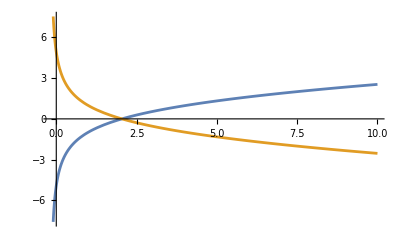

```mathematica
Plot[{μ1pos,μ1neg},{δ,δ0,10}]
```

```mathematica
amplitude+O[ξ]
```

(2 Sin[r/2]^2)/(√r √ξ)+((8 r Λ1 Sin[r/2]^2-8 r^2 Λ1 Sin[r]) √ξ)/(4 r^(3/2))+O[ξ]^1

```mathematica
N[(2 Sin[r/2]^2)/(√r √ξ)/.{r->1.1655611852072119,ξ-> 1/100}]
```

5.61095